```mathematica
(*fetch file name*)
SetDirectory[NotebookDirectory[]];
filepath=SystemDialogInput["FileOpen",NotebookDirectory[],WindowTitle->"choose time domain file"];
(*import time domain data*)
timeDomainData=Import[filepath];
(*calculate power spectrum*)
tempData=Abs[Fourier[timeDomainData[[All,2]]]]^2;
(*transform to single sided format, ie. remove redundant halve of data*)
dataRange={1,Length[tempData]/2-1};
spectralData=Take[tempData,dataRange];
(*remove huge DC component*)
spectralData[[1]]=0;
(*calculate frequency values and prepare export*)
tempExportData=Riffle[Table[1/(25*10^-12*Length[tempData])*i//N,{i,0,Length[spectralData]}],spectralData];
(*export data*)
exportData=Partition[tempExportData,2];
Export["exportData.dat",exportData];
(*plot data to check*)
ListPlot[timeDomainData[[All,2]], Joined->True,PlotRange->All]
ListLinePlot[spectralData,PlotRange->All,DataRange->{0,1/(25*10^-12*Length[tempData])*Length[spectralData]}]
Sound[SoundNote[#,0.5, "Polysynth"]&/@{2,4,0,-12,-5},1];
EmitSound[%]
```

-Graphics-

-Graphics-

-Graphics-

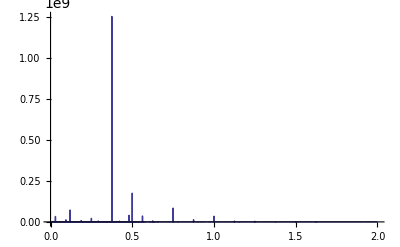

800000

100000

```mathematica
(*fetch file name*)
SetDirectory[NotebookDirectory[]];
filepath=SystemDialogInput["FileOpen",NotebookDirectory[],WindowTitle->"choose time domain file"];
(*import time domain data*)
timeDomainData=Import[filepath];
reducedTimeDomainData=Drop[timeDomainData,Length[timeDomainData]-Length[timeDomainData]/8];
(*calculate power spectrum*)
tempData=Abs[Fourier[reducedTimeDomainData[[All,2]]]]^2;
(*transform to single sided format, ie. remove redundant halve of data*)
dataRange={1,Length[tempData]/2-1};
spectralData=Take[tempData,dataRange];
(*remove huge DC component*)
spectralData[[1]]=0;
(*calculate frequency values and prepare export*)
tempExportData=Riffle[Table[1/(25*10^-12*Length[tempData])*i//N,{i,0,Length[spectralData]}],spectralData];
(*export data*)
exportData=Partition[tempExportData,2];
Export["exportData.dat",exportData];
(*plot data to check*)
ListPlot[timeDomainData[[All,2]], Joined->True,PlotRange->All]
ListLinePlot[spectralData,PlotRange->All,DataRange->{0,1/(25*10^-12*Length[tempData])*Length[spectralData]}]
Length[timeDomainData]
Length[tempData]
Sound[SoundNote[#,0.5, "Polysynth"]&/@{2,4,0,-12,-5},1];
EmitSound[%]
```